```mathematica
p/(2Pi)*Integrate[(a+b*Cos[k]+c*Cos[k]^2)/(x+y*Cos[k]+z*Cos[k]^2),k]
```

(p (c k+(√2 (c (y^2-2 x z+y √(y^2-4 x z))+z (2 a z-b (y+√(y^2-4 x z)))) ArcTanh[((y-2 z+√(y^2-4 x z)) Tan[k/2])/(√(-2 y^2+4 z (x+z)-2 y √(y^2-4 x z)))])/(√(y^2-4 x z) √(-y^2+2 z (x+z)-y √(y^2-4 x z)))-(√2 (c (-y^2+2 x z+y √(y^2-4 x z))+z (-2 a z+b (y-√(y^2-4 x z)))) ArcTanh[((-y+2 z+√(y^2-4 x z)) Tan[k/2])/(√(-2 y^2+4 z (x+z)+2 y √(y^2-4 x z)))])/(√(y^2-4 x z) √(-y^2+2 z (x+z)+y √(y^2-4 x z)))))/(2 π z)

```mathematica
NIntegrate[p/(2Pi)(a+b*Cos[k]+c*Cos[k]^2)/(x+y*Cos[k]+z*Cos[k]^2),{k,-Pi,Pi}]/.{a->Jtwo,b->Jone,c->2Jtwo,x->J^2-2J*Jtwo-z^2,y->2*J*Jone,z->4J*Jtwo}
```

NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-z^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.1,Jtwo,-0.1,z]-G22[1,0.1,Jtwo,-0.1,z]-G12[1,0.1,Jtwo,-0.1,z]^2+G11[1,0.1,Jtwo,-0.1,z]G22[1,0.1,Jtwo,-0.1,z]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
√(J^4/(J^2+J a)+(J^3 a)/(J^2+J a)+(J^2 a^2)/(2 (J^2+J a))+(J a^3)/(8 (J^2+J a))-1/(8 (J^2+J a))(√(256 J^4 J q^2+512 J^3 J q^2 a+64 J^6 a^2+320 J^2 J q^2 a^2+96 J^5 a^3+64 J  J q^2 a^3+52 J^4 a^4+12 J^3 a^5+J^2 a^6)))/.{J->1,q->0.1,a->2*-0.1}
```

0.8545

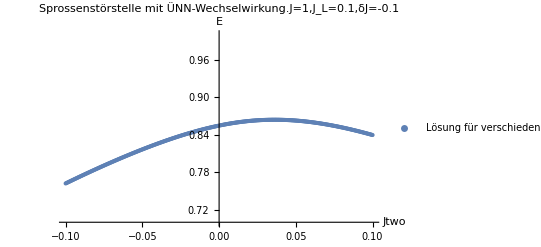

```mathematica
P = ListPlot[Fueger[moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]],moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]],AxesLabel->{Jtwo,"E"},PlotRange->{0.7,1},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.1"]
```

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

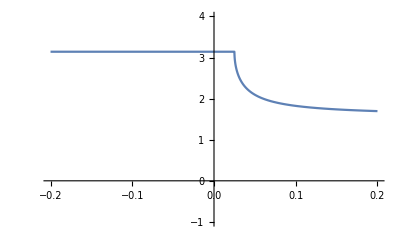

```mathematica
Plot[Inv[0.1,Jtwo],{Jtwo,-0.2,0.2},PlotRange->{-1,4}]
```

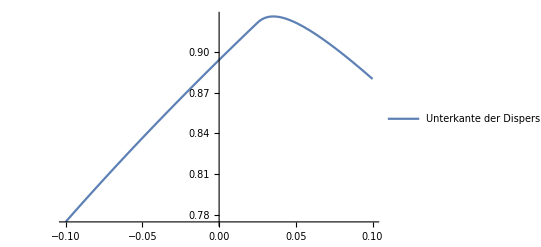

```mathematica
G = Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1},PlotLegends->{"Unterkante der Dispersion"}]
```

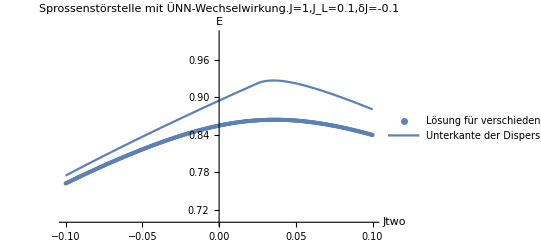

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.1,{{-0.005,0.8518170212146641},{-0.01,0.8488372997456294},{-0.015,0.8455788532760256},{-0.02,0.8420600465393536},{-0.025,0.8382990565930841},{-0.03,0.8343134421054639},{-0.035,0.8301198271341518},{-0.04,0.8257336909812681},{-0.045,0.8211692487208532},{-0.05,0.816439404137469},{-0.055,0.8115557569346296},{-0.06,0.8065286479886997},{-0.065,0.8013672291799866},{-0.07,0.7960795472625412},{-0.075,0.7906726339386496},{-0.08,0.7851525966034867},{-0.085,0.7795247060577173},{-0.09,0.7737934788817714},{-0.095,0.7679627531841818},{-0.1,0.7620357571513292}}]
```

{{-0.005,0.0370024},{-0.01,0.0343388},{-0.015,0.0319176},{-0.02,0.0297197},{-0.025,0.0277263},{-0.03,0.0259191},{-0.035,0.0242805},{-0.04,0.0227944},{-0.045,0.0214457},{-0.05,0.0202206},{-0.055,0.0191066},{-0.06,0.0180925},{-0.065,0.017168},{-0.07,0.0163243},{-0.075,0.0155531},{-0.08,0.0148474},{-0.085,0.0142007},{-0.09,0.0136073},{-0.095,0.0130622},{-0.1,0.0125609}}

```mathematica
differ[1,0.1,{{0.005,0.8545000070855844},{0.01,0.8589093531704773},{0.015,0.8606073725318385},{0.02,0.8619532730957528},{0.025,0.8629404859227445},{0.03,0.8635661785075325},{0.035,0.8638313182322822},{0.04,0.8637405121390841},{0.045,0.8633016514146582},{0.05,0.8625254108557843},{0.055,0.8614246641766539},{0.06,0.8600138750800655},{0.065,0.8583085143122512},{0.07,0.8563245384271406},{0.075,0.8540779508668574},{0.08,0.8515844524689898},{0.085,0.8488591789933743},{0.09,0.8459165167027465},{0.095,0.8427699840064636},{0.1,0.8394321663097011}}]
```

{{0.005,0.0455},{0.01,0.0466292},{0.015,0.050436},{0.02,0.0545619},{0.025,0.255094},{0.03,0.0619967},{0.035,0.06276},{0.04,0.0622724},{0.045,0.06106},{0.05,0.059429},{0.055,0.0575669},{0.06,0.0555916},{0.065,0.0535788},{0.07,0.0515773},{0.075,0.0496182},{0.08,0.0477208},{0.085,0.0458968},{0.09,0.0441521},{0.095,0.0424894},{0.1,0.0409087}}

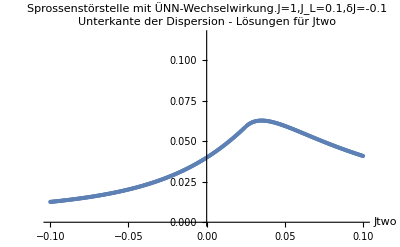

```mathematica
ListPlot[Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]]],differ[1,0.1,moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.1"]
```